# Network Map Animation Routines :: HMSC

## Functions

```mathematica
<<PajaroLocoPublic`
<<Utilities`CleanSlate`
SetDirectory[NotebookDirectory[]]
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
GraphMap2[{raw_,coordsRaw_,rawPop_,name_,pad_},maxTransitionsSize_,imageSize_,cityScaler_,cityScaler2_]:=Module[{coords,head,data,pops,popsVct,sizes,edgeshape,graph,coordSizePairs,points},
{coords,head,data,pops}={
coordsRaw[[2;;All,2;;All]],
raw[[1]][[2;;All]],
Chop[raw[[2;;All,2;;All]]],
rawPop[[2;;All,2]]
};
(**)
popsVct=Log/@(1+Rescale[#,{Min[pops],Max[pops]/10}]&/@pops//N);
sizes=(ToString[#[[1]]]->(cityScaler*#[[2]]))&/@Transpose[{Range[1,popsVct//Length],popsVct}];
(**)
coordSizePairs=Transpose[{coords,sizes}];
points=Disk[#[[1]],#[[2,2]]/cityScaler2]&/@coordSizePairs;
(*Print[points];
Graphics[points]*)
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]};
graph=GraphTransitionsFrequenciesWithMax[{data,ToString/@Range[data//Length]},maxTransitionsSize,VertexLabelStyle->Opacity[0],
EdgeShapeFunction->edgeshape,
VertexCoordinates->coords,
VertexSize->.00001,
VertexStyle->{{EdgeForm[None],Black}},
ImageSize->imageSize,
LineThickness->.025,
VariableStyle->"LineWidth",
Prolog->Flatten[{EdgeForm[{Black,Thickness[.005]}],White,CountryData["Comoros",{"FullPolygon","Equirectangular"}],Flatten[{Darker[White,1],points}]}],
Epilog->Flatten[{Darker[White,1],points}],
ImagePadding->pad
];
graph
]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding]
]
]
MapNetworkWithGenotypes[{countryMap_,cityCoordinates_},{transitionsMatrix_,nodeNames_},{nodesShapes_,nodesSizes_},{imageSize_,nodeScaler_,maxTransitionsSize_,padding_,lineWidth_}]:=Module[{},
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]};
GraphTransitionsFrequenciesWithMax[transitionsMatrix,maxTransitionsSize,
VertexLabelStyle->Opacity[0],
EdgeShapeFunction->edgeshape,
VertexCoordinates->cityCoordinates,
VertexSize->nodesSizes,
VertexShape->nodesShapes,
ImageSize->imageSize,
LineThickness->lineWidth,
VariableStyle->"LineWidth",
ImagePadding->padding,
Prolog->Flatten[{EdgeForm[{Black,Thickness[.005]}],White,countryMap}]
]
]
ListLinePlotPopulation[mosyPop_,genotypes_,{plotRange_,colors_,imageSize_},label_]:=ListLinePlot[Append[mosyPop//Transpose,Total/@mosyPop],
PlotLegends->Append[genotypes,"Total"],
PlotRange->plotRange,
ImageSize->imageSize,
Frame->True,
PlotLabel->Style[label,20,Black],
FrameStyle->Thick,
GridLines->Automatic,
PlotStyle->(Append[{Opacity[.9],Thickness[.02]},#]&/@colors),
FrameTicksStyle->Directive[Gray,12],
FrameLabel->(Style[#,12.5,Black]&/@{"Time","Population"})
]
```

/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/R/ComorosTest

## Static Map Routine

```mathematica
citiesDummy=Accumulate[RandomReal[{-1,1},{50,2}]];
names=ToString/@Range[citiesDummy//Length];
pops=RandomInteger[1000,citiesDummy//Length];
cities=Transpose[{names,citiesDummy,pops}];
ListPlot[Table[Callout[citiesDummy[[i]],i],{i,1,Length[citiesDummy]}]]
```

```mathematica
distancesMatrix=Table[
EuclideanDistance[cities[[i,2]],#]&/@cities[[All,2]]
,{i,1,cities//Length}];
fixed=ReplaceAll[#,ComplexInfinity->0]&/@Quiet[(1/distancesMatrix)];
thresheld=Table[If[#>.75,#,0]&/@i,{i,fixed}];
headedMatrix=Prepend[Prepend[thresheld,cities[[All,1]]]//Transpose,Prepend[cities[[All,1]],""]]//Transpose;
MatrixPlot[thresheld]
headedMatrix=Prepend[Prepend[thresheld//UpperTriangularize,cities[[All,1]]]//Transpose,Prepend[cities[[All,1]],""]]//Transpose;
(*Export["./Comoros.pdf",map,"ImageEncoding"->"LZW"]*)
```

## Export

```mathematica
(*Export["citiesRandom.csv",Flatten/@cities]
transitionsMatrix=(#/Total[#])&/@ReplacePart[thresheld,{i_,i_}->1000];
MatrixPlot[transitionsMatrix]
headedMatrix=Prepend[Prepend[transitionsMatrix//UpperTriangularize,cities[[All,1]]]//Transpose,Prepend[cities[[All,1]],""]]//Transpose;
Export["transitionsRandom.csv",transitionsMatrix]*)
```

## Load Data

```mathematica
dataPath="./RandomTestNR/";
dataRange={1920,1999};
scaler=3.5;
size={2560,1440};
resolution=500;
(*Load Datasets*)
names=FileNames["ADM_PATCH*.csv",dataPath]//Sort;
dataSets=ParallelMap[Import[#][[2;;All,2;;All]]&,names];
genotypes=Import[names[[1]]][[1,2;;All]];
geneLength=Length[genotypes]-2;
genotypes=genotypes[[1;;geneLength]];
dataSets=#[[All,1;;geneLength]]&/@dataSets;
ticksMax=Length[dataSets[[1]]];
range=Range[dataSets//Length];
maxPop=Flatten[dataSets]//Max;
(*Define Colors Palette*)
steps=(genotypes//Length)-1;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/steps],Black}//Flatten
(**)
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import["citiesRandom.csv"];
transitionsMatrixIn=Import["transitionsRandom.csv"];
MatrixPlot[transitionsMatrixIn];
```

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.45565900000000004, 0.33950076, 0.7574642],RGBColor[0.603583, 0.5914516, 0.9104053999999999],RGBColor[0.722869, 0.7831114, 0.9131246000000001],RGBColor[0.8340489999999999, 0.870814, 0.8820358],RGBColor[0.941176, 0.906538, 0.834043],GrayLevel[0]}

## Pre - Process Frames (Pie Charts)

```mathematica
frames=Table[
ParallelMap[{
PieChart[#,ChartStyle->colors(*({Opacity[.95],#}&/@colors)*),BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&,i]
,{i,(dataSets//Transpose)[[dataRange[[1]];;dataRange[[2]]]]}];
```

```mathematica
timeFrames=(frames//Transpose);
scaledSizesTimeFrames=Table[{#[[1]],#[[2]]/maxPop}&/@i,{i,timeFrames}]//Transpose;
```

## Pre - Process Frames (Sector Chart)

```mathematica
sectorPlotsA=ParallelTable[
timeStep=i;
SectorChart[Reverse[Transpose[Transpose[{Append[ConstantArray[1,Length[#]],.0001],Append[#,Total[#]]}]&/@timeStep]],
ChartStyle->{Reverse[colors],None},
ChartBaseStyle->EdgeForm[Thin],
PolarGridLines->{Range[0,2Pi,2π/Length[timeStep]],None(*Range[0,10,0.5]*)},
GridLinesStyle->Directive[Gray,Opacity[.25],Thin],
PolarAxes->False(*{True,False}*),
PolarTicks->None,
AxesStyle->Directive[Opacity[.25]],
PerformanceGoal->"Speed",
SectorOrigin->{{Pi,"Clockwise"},0}
]
,{i,(dataSets//Transpose)[[dataRange[[1]];;dataRange[[2]]]]}];
sectorPlotsB=ParallelTable[
timeStep=i;
SectorChart[Transpose[{Append[ConstantArray[1,Length[#]],.0001],Append[#,Total[#]]}]&/@timeStep,
ChartStyle->colors,
ChartBaseStyle->EdgeForm[None],
PolarGridLines->{Range[0,2Pi,2π/(Length[genotypes])],None(*Range[0,10,0.5]*)},
GridLinesStyle->Directive[Gray,Opacity[.25],Thin],
PolarAxes->False(*{True,False}*),
PolarTicks->None,
AxesStyle->Directive[Opacity[.25]],
(*ChartLegends->((#[[1]]<>":"<>StringPadLeft[ToString[Round[#[[2]]]],6,"0"])&/@Append[{genotypes,Total/@(timeStep//Transpose)}//Transpose,{"Total",Total[Total/@(timeStep//Transpose)]}]),*)
PerformanceGoal->"Speed",
SectorOrigin->{{Pi,"Clockwise"},0}
]
,{i,(dataSets//Transpose)[[dataRange[[1]];;dataRange[[2]]]]}];
(*Table[
Export[NotebookDirectory[]<>"/Frames/SectorTest/Agraph"<>StringPadLeft[ToString[i+dataRange[[1]]-1],5,"0"]<>".png",sectorPlotsA[[i]]];
Export[NotebookDirectory[]<>"/Frames/SectorTest/Bgraph"<>StringPadLeft[ToString[i+dataRange[[1]]-1],5,"0"]<>".png",sectorPlotsB[[i]]];
,{i,1,Length[frames]}];*)
```

## Pre - Process Frames (PopDynamics)

```mathematica
totalPops=Table[Total[dataSets[[All,i]]],{i,1,ticksMax}];
max=Max[totalPops//Flatten];
(*Uper corner*)
popDynPlotsTotal=Table[
set=totalPops[[1;;i]];
llPop=ListLinePlotPopulation[set,genotypes,{{{0,ticksMax},{0,13000}},colors,275},""]
,{i,dataRange[[1]],dataRange[[2]]}];
(*Lower corner*)
patch=1;
popDynPlots=Table[
set=dataSets[[patch]][[1;;i]];
llPop=ListLinePlotPopulation[set,genotypes,{{{0,ticksMax},{0,1200}},colors,250},"Releases Site"]
,{i,dataRange[[1]],dataRange[[2]]}];
```

## Pre - Process Frames (Counts)

```mathematica
countsFrames=Table[
{
Style[#,20]&/@genotypes,
Style[Round[#],20,Gray]&/@Threshold[dataSets[[All,i]]//Total,{"Hard",10^-1}]
}//Transpose//Grid[Append[#,{Style["Total",20],Style[dataSets[[All,i]]//Total//Total//Round,20]}],Frame->True,FrameStyle->Thick,ItemSize->7,Background->{None,Append[Opacity[.25,#]&/@colors,Black]}]&
,{i,dataRange[[1]],dataRange[[2]]}];
countsFrames[[1]]
```

HH | 0
Hh | 0
HR | 0
hh | 0
hR | 0
RR | 0
Total | 0

## Network Frames

## Probe

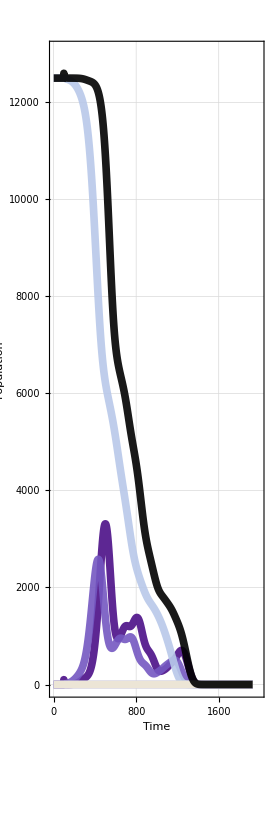
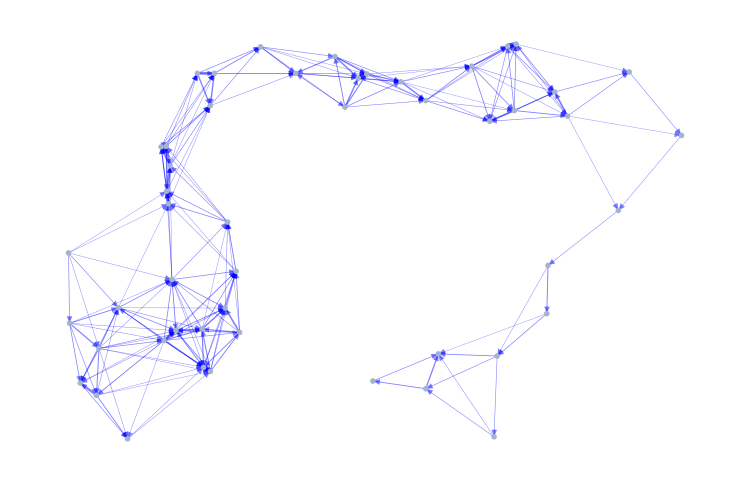
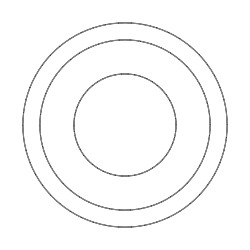
-Graphics- | -Graphics-Time: 1929HMSC,SLW,JB,JM | -Graphics-
HH | 0
Hh | 0
HR | 0
hh | 0
hR | 0
RR | 0
Total | 0
-Graphics-

```mathematica
tick=10;
(**)
rangeTick=Range[dataRange[[1]],dataRange[[2]]];
range=Range[dataSets//Length];
transitionsMatrix={transitionsMatrixIn,ToString/@range};
vertexCoordinates={#[[1]],#[[2]]}&/@Reverse/@cities[[All,2]];
transMatrix={ReplacePart[Chop[transitionsMatrix[[1]]//UpperTriangularize],{i_,i_}->0],transitionsMatrix[[2]]};
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,1]]}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->scaler*#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,2]]}]];
vertexCoordinates=Reverse[{#[[1]],#[[2]]}]&/@cities[[All,2]];
transitionsMatrixB={transitionsMatrix,ToString/@range};
(*GRAPH*)
graph=GraphTransitionsFrequenciesWithMax[transMatrix,.001,
VertexCoordinates->vertexCoordinates,
VertexShape->vertexShapes,
VertexSize->vertexSizes,
LineThickness->.0005,
VariableStyle->"LineWidth",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->750
(*Prolog->Flatten[{EdgeForm[{Black,Opacity[.9],Thickness[.015]}],White,countryMap}],*)
(*ImagePadding->{{320,320},{10,10}}*)
];
Grid[{{
Grid[{
{
Grid[{{Show[popDynPlotsTotal[[tick]][[1]],AspectRatio->3]}},Alignment->Center],
Overlay[{
Overlay[{
graph,
Style[ToString["Time: "]<>ToString[rangeTick[[tick]]],Gray,20]
},Alignment->{0,0}],
Style["HMSC,SLW,JB,JM",Gray,.0001]
},Alignment->{.3,-.75}]
}
}],
Grid[{{Show[sectorPlotsA[[tick]],ImageSize->250]},{countsFrames[[tick]]},{Show[sectorPlotsB[[tick ]],ImageSize->250]},{}}]
}}]
```

## Export

```mathematica
(**)
rangeTick=Range[dataRange[[1]],dataRange[[2]]];
range=Range[dataSets//Length];
transitionsMatrix={transitionsMatrixIn,ToString/@range};
vertexCoordinates={#[[1]],#[[2]]}&/@Reverse/@cities[[All,2]];
transMatrix={ReplacePart[Chop[transitionsMatrix[[1]]//UpperTriangularize],{i_,i_}->0],transitionsMatrix[[2]]};
Table[
tick=i;
(**)
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,1]]}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->scaler*#[[2]]}&/@Transpose[{range,scaledSizesTimeFrames[[tick]][[All,2]]}]];
(*GRAPH*)
graph=GraphTransitionsFrequenciesWithMax[transMatrix,.001,
VertexCoordinates->vertexCoordinates,
VertexShape->vertexShapes,
VertexSize->vertexSizes,
LineThickness->.0005,
VariableStyle->"LineWidth",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->1000,
(*Prolog->Flatten[{EdgeForm[{Black,Opacity[.9],Thickness[.015]}],White,countryMap}],*)
ImagePadding->{{0,0},{25,25}}
];
overlay=
Grid[{{Style["",50]},{Style["MGDrivE",50]},{Style["",50]},
{Grid[{{
Grid[{
{
Grid[{{Show[popDynPlotsTotal[[tick]][[1]],AspectRatio->3]}},Alignment->Center],
Overlay[{
Overlay[{
graph,
Style[ToString[rangeTick[[tick]]],Gray,20]
},Alignment->{0,0}],
Style["HMSC,SLW,JB,JM",Gray,.0001]
},Alignment->{.3,-.75}]
}
}],
Grid[{{Show[sectorPlotsA[[tick]],ImageSize->250]},{countsFrames[[tick]]},{Show[sectorPlotsB[[tick ]],ImageSize->250]},{}}]
}}]},{Style["",100]}}];
Export[NotebookDirectory[]<>"/Frames/graph"<>StringPadLeft[ToString[i+dataRange[[1]]-1],5,"0"]<>".png",
overlay,
ImageResolution->resolution,
ImageSize->{2*3840,2*2160}
];
Clear[graph,overlay];
,{i,1,dataRange[[2]]-dataRange[[1]]}];
```

## Development

```mathematica
timeStep=Transpose[dataSets][[1165]];
ts=timeStep[[1]]
SectorChart[Transpose[{Range[ts//Length],ts}],PolarGridLines->Automatic,PolarAxes->Automatic,ChartStyle->colors,ChartLegends->genotypes]
```

```mathematica
SectorChart[Transpose[Transpose[{Append[ConstantArray[1,Length[#]],.001],Append[#,maxPop]}]&/@timeStep],
ChartStyle->colors,
ImageSize->1000,
PolarGridLines->{Range[0,2Pi,2π/Length[genotypes]],Range[0,10,0.5]},
GridLinesStyle->Directive[Gray],
PolarAxes->{True,False},
PolarTicks->None,
AxesStyle->Directive[White],
ChartLegends->genotypes,
PerformanceGoal->"Speed",
SectorOrigin->{{Pi,"Clockwise"},0}
]
```